# Composite Numerical Integration

In practice we get much better estimates if we divide the interval [a,b] and apply a quadrature formula on each interval.

Let’s define our two quadrature formulas again.

```mathematica
Trap[f_,a_,b_]:=Module[{h,x0=a,x1=b,M,x},
h=b-a;
M=Maximize[{f''[x],x0≤x≤x1},x];
{N[(h/2)*(f[x0]+f[x1])],N[Abs[h^3/12*M][[1]]]}
]
```

```mathematica
Simpson[f_,a_,b_]:=Module[{x0=a,,x1,x2=b,h=(b-a)/2,M,x},
x1=x0+h;
M=Maximize[{f'''[x],x0≤x≤x2},x];
{N[(h/3)*(f[x0]+4f[x1]+f[x2])],N[Abs[h^5/90*M][[1]]]}
]
```

Since we have code that will estimate the integral over an arbitrary interval we can simply cut [a,b] into n equal intervals and sum the results of the quadrature formula. Note that we are using the linearity of the integral here. Also, the total error is just the sum of the error on each subinterval.

```mathematica
CompTrap[f_,a_,b_,n_]:=Module[{h},
h=(b-a)/n;
A[i_]:=a+i*h;
B[i_]:=a+(i+1)h;
Sum[Trap[f,A[i],B[i]],{i,0,n-1}]
]
```

```mathematica
CompSimp[f_,a_,b_,n_]:=Module[{h},
h=(b-a)/n;
A[i_]:=a+i*h;
B[i_]:=a+(i+1)h;
Sum[Simpson[f,A[i],B[i]],{i,0,n-1}]
]
```

Now let’s pick a function and take a look!

```mathematica
f[x_]:=x*Sin[x]
```

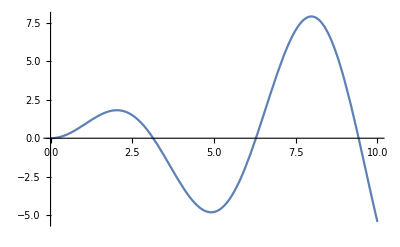

```mathematica
Plot[f[x],{x,0,10}]
```

So we can take a look at the interpolating polynomials we can make a Table of them!

```mathematica
Linears[f_,a_,b_,n_]:=Table[Piecewise[{{
InterpolatingPolynomial[{{a+i*(b-a)/n,f[a+i*(b-a)/n]},{a+(i+1)*(b-a)/n,f[a+(i+1)*(b-a)/n]}},x],a+i*(b-a)/n≤x<=a+(i+1)*(b-a)/n}}],{i,0,n-1}];
```

```mathematica
Manipulate[Plot[{Linears[f,0,10,n],f[x]},{x,0,10},Filling->Axis,PlotRange->All],{n,1,20,1}]
```

Estimating the intergral using the Composite Trapezoid Rule is as easy as calling our function

```mathematica
Manipulate[CompTrap[f,0,10,n],{n,1,20,1}]
```

```mathematica
Quads[f_,a_,b_,n_]:=Table[Piecewise[{{
InterpolatingPolynomial[{{a+i*(b-a)/n,f[a+i*(b-a)/n]},{((a+i*(b-a)/n)+(a+(i+1)*(b-a)/n))/2,f[((a+i*(b-a)/n)+(a+(i+1)*(b-a)/n))/2]},{a+(i+1)*(b-a)/n,f[a+(i+1)*(b-a)/n]}},x],a+i*(b-a)/n≤x<=a+(i+1)*(b-a)/n}}],{i,0,n-1}];
```

```mathematica
Manipulate[Plot[{Quads[f,0,10,n],f[x]},{x,0,10},Filling->Axis,PlotRange->All],{n,1,20,1}]
```

```mathematica
Manipulate[CompSimp[f,0,10,n],{n,1,20,1}]
```

To answer questions like “how many subdivisions should we take to get error less than ϵ?” we need to do some work to get a single error term over the whole interval in terms of n (well really in terms of h).